## Parameters

```mathematica
i[k_,nn_]:=(nn+1-k)/nn
ϕe[k_]:=(k-1) Pi/2
```

## Maximum and min of the current

### The maximum is

```mathematica
Sum[i[k,nn],{k,1,nn}]
```

(1+nn)/2

### We know that the efficiency is (nn-1)/(nn+1), thus the minimum is

```mathematica
Solve[(nn-1)/(nn+1)==(nn+1-2x)/(nn+1+2x),x]
```

{{x→(1+nn)/(2 nn)}}

## Analytical form

```mathematica
f[ϕ_,nn_]=Sum[i[k,nn]Sin[k ϕ-ϕe[k]],{k,1,nn}]//FullSimplify
```

-(-nn+(1+nn) Sin[ϕ]+Sin[(nn π)/2-(1+nn) ϕ])/(2 nn (-1+Sin[ϕ]))

```mathematica
fleveled[ϕ_,nn_]=f[ϕ,nn]+(1+nn)/(2nn)//FullSimplify
```

(1+Sin[(nn π)/2-ϕ-nn ϕ])/(2 nn-2 nn Sin[ϕ])

```mathematica
f2[ϕ_,nn_]=Sum[i[k,nn]Cos[k ϕ],{k,1,nn}]//FullSimplify
```

(nn-(1+nn) Cos[ϕ]+Cos[(1+nn) ϕ])/(2 nn (-1+Cos[ϕ]))

```mathematica
f2leveled[ϕ_,nn_]=f2[ϕ,nn]+(1+nn)/(2nn)//FullSimplify//TrigExpand//FullSimplify
```

(-1+Cos[(1+nn) ϕ])/(-2 nn+2 nn Cos[ϕ])

```mathematica
f3[ϕ_,nn_]=(-1+Cos[(1+nn) (ϕ-Pi/2)])/(-2 nn+2 nn Sin[ϕ])-(1+nn)/(2nn)
```

-(1+nn)/(2 nn)+(-1+Cos[(1+nn) (-π/2+ϕ)])/(-2 nn+2 nn Sin[ϕ])

```mathematica
Manipulate[Plot[{f[ϕ Pi,nn],f3[ϕ Pi,nn],(nn+1)/2,-(1+nn)/(2nn)},{ϕ,-1,1}],{nn,2,100,1}]
```

## Flux configurations

```mathematica
nk[1,nn]
```

(nn!)/(Floor[nn/2]!)

```mathematica
nk[k_,nn_]:=(nn!)/(Floor[nn/2]! k)
```

```mathematica
ϕext[k_,nn_]:=(k-1)/4 nk[k,nn]
```

```mathematica
ϕloop[k_,nn_]:=ϕext[k+1,nn]-ϕext[k,nn]
```

```mathematica
ϕext[2,3]
```

3/4

```mathematica
For[NN=1,NN<8,NN++,
Print@Table[ϕext[kk,NN],{kk,1,NN}]
]
```

{0}

{0,1/4}

{0,3/4,1}

{0,3/2,2,9/4}

{0,15/2,10,45/4,12}

{0,15,20,45/2,24,25}

{0,105,140,315/2,168,175,180}

```mathematica
For[NN=1,NN<8,NN++,
Print@Differences@Table[ϕext[kk,NN],{kk,1,NN}]
]
```

{}

{1/4}

{3/4,1/4}

{3/2,1/2,1/4}

{15/2,5/2,5/4,3/4}

{15,5,5/2,3/2,1}

{105,35,35/2,21/2,7,5}

```mathematica
For[NN=2,NN<8,NN++,
Print@Table[ϕloop[kk,NN],{kk,1,NN-1}]
]
```

{1/4}

{3/4,1/4}

{3/2,1/2,1/4}

{15/2,5/2,5/4,3/4}

{15,5,5/2,3/2,1}

{105,35,35/2,21/2,7,5}

```mathematica
For[NN=2,NN<8,NN++,
Print@Table[(NN!)/(4 (kk+kk^2) Floor[NN/2]!),{kk,1,NN-1}]
]
```

{1/4}

{3/4,1/4}

{3/2,1/2,1/4}

{15/2,5/2,5/4,3/4}

{15,5,5/2,3/2,1}

{105,35,35/2,21/2,7,5}

```mathematica
NN=.;ϕloop[k,NN]//FullSimplify
```

(NN!)/(4 (k+k^2) Floor[NN/2]!)

```mathematica
For[NN=1,NN<11,NN++,
Print@Table[nk[kk,NN],{kk,1,NN}]
]
```

{1}

{2,1}

{6,3,2}

{12,6,4,3}

{60,30,20,15,12}

{120,60,40,30,24,20}

{840,420,280,210,168,140,120}

{1680,840,560,420,336,280,240,210}

{15120,7560,5040,3780,3024,2520,2160,1890,1680}

{30240,15120,10080,7560,6048,5040,4320,3780,3360,3024}

```mathematica
For[NN=1,NN<8,NN++,
Print@Table[nk[kk,NN],{kk,1,NN}]
]
```

```mathematica
For[NN=1,NN<8,NN++,
Print@Table[(NN+1-kk)/N,{kk,1,NN}]
]
```

{1/N}

{2/N,1/N}

{3/N,2/N,1/N}

{4/N,3/N,2/N,1/N}

{5/N,4/N,3/N,2/N,1/N}

{6/N,5/N,4/N,3/N,2/N,1/N}

{7/N,6/N,5/N,4/N,3/N,2/N,1/N}

```mathematica
s
```

```mathematica
For[NN=1,NN<8,NN++,
Print[(NN-1)/(NN+1)]
]
```

0

1/3

1/2

3/5

2/3

5/7

3/4

```mathematica
Differences[{1,2,5}]
```

{1,3}

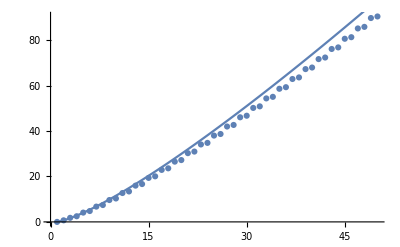

```mathematica
NNmax=50;Show[
{ListPlot[Table[Log[nk[1,NN]],{NN,1,NNmax}]],
Plot[Log[Exp[NN/2 Log[NN]]],{NN,1,NNmax}]}]
```

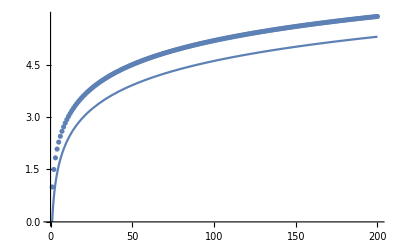

```mathematica
NNmax=200;Show[
{ListPlot[Table[HarmonicNumber[NN],{NN,1,NNmax}]],
Plot[Log[NN],{NN,1,NNmax}]}]
```

```mathematica
Sum[1/x,{x,1,nn}]
```

HarmonicNumber[nn]

```mathematica
x!/(x/2)!//FullSimplify
```

(x!)/(x/2!)

```mathematica
efficiency[a_,b_]:=(Abs[Abs[a]-Abs[b]])/(Abs[a]+Abs[b])
```

```mathematica
min=Minimize[{Cos[x]+Cos[2x],-Pi<x<Pi},x][[1]]
max=Maximize[{Cos[x]+Cos[2x],-Pi<x<Pi},x][[1]]
efficiency[max,min]//N
```

Cos[2 ArcTan[√(5/3)]]+Cos[4 ArcTan[√(5/3)]]

2

0.28

```mathematica
7/25//N
```

0.28

```mathematica
efficiency[0.63372,0.8032781564427135]
```

0.117995

```mathematica
efficiency[0.671502,0.8283998701720222]
```

0.104605

```mathematica
Subscript[n, k]=(N!)/(Subscript[Π, p ∈ Prime] Floor[N/p]!)1/k
```

```mathematica
Factorial[0]
```

1

```mathematica
Integrate[(nn-(1+nn) Cos[ϕ]+Cos[(1+nn) ϕ])/(2 nn (-1+Cos[ϕ])),ϕ]
```

1/(2 nn^2 (2+nn) (-1+Cos[ϕ]))ⅇ^(-ⅈ (1+nn) ϕ) Sin[ϕ/2] (-ⅈ nn (2+nn) Hypergeometric2F1[1,-1-nn,-nn,ⅇ^(ⅈ ϕ)] Sin[ϕ/2]-ⅈ ⅇ^(ⅈ ϕ) (2+3 nn+nn^2) Hypergeometric2F1[1,-nn,1-nn,ⅇ^(ⅈ ϕ)] Sin[ϕ/2]+nn (-ⅈ ⅇ^(2 ⅈ (1+nn) ϕ) (2+nn) Hypergeometric2F1[1,1+nn,2+nn,ⅇ^(ⅈ ϕ)] Sin[ϕ/2]-ⅈ ⅇ^(ⅈ (3+2 nn) ϕ) (1+nn) Hypergeometric2F1[1,2+nn,3+nn,ⅇ^(ⅈ ϕ)] Sin[ϕ/2]+(2+nn) (-(-1+ⅇ^(ⅈ (1+nn) ϕ))^2 Cos[ϕ/2]+2 ⅇ^(ⅈ (1+nn) ϕ) (1+nn) ϕ Sin[ϕ/2])))

```mathematica
Manipulate[Plot[Sum[-i[k,10]/k Cos[k ϕ-ϕe[k]],{k,1,10}]+ii ϕ,{ϕ,-10,10}],{{ii,0},-20,20}]
```

```mathematica
Sum[-i[k,nn]/k Cos[k ϕ-ϕe[k]],{k,1,10}]
```

-Cos[ϕ]+((-2+nn) Cos[3 ϕ])/(3 nn)-((-4+nn) Cos[5 ϕ])/(5 nn)+((-6+nn) Cos[7 ϕ])/(7 nn)-((-8+nn) Cos[9 ϕ])/(9 nn)-((-1+nn) Sin[2 ϕ])/(2 nn)+((-3+nn) Sin[4 ϕ])/(4 nn)-((-5+nn) Sin[6 ϕ])/(6 nn)+((-7+nn) Sin[8 ϕ])/(8 nn)-((-9+nn) Sin[10 ϕ])/(10 nn)